# HighPT

## Flavor bounds from high-p_T tails at LHC

## Preamble

#### Set package directory

Make sure that the package directory is in the $Path.

```mathematica
SetDirectory@ ParentDirectory@ NotebookDirectory[];
(*AppendTo[$Path, "/path/to/HighPT"];*)
```

#### Loading the package

```mathematica
<<HighPT`
```

-Graphics-

Authors: Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo, Olcyr Sumensari, and Felix Wilsch

References: arXiv:22xx.xxxxxhttps://arxiv.org/Nonehttps://arxiv.org/HyperlinkHyperlinkActive, arXiv:22xx.xxxxxhttps://arxiv.org/Nonehttps://arxiv.org/HyperlinkHyperlinkActive

Website: https://github.com/HighPT/HighPThttps://github.com/HighPT/HighPTNonehttps://github.com/HighPT/HighPTHyperlinkHyperlinkActive

HighPT is free software released under the terms of the MIT License.

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

#### Load MaTeX` for LATEX labels

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{dsfont,amsmath}","\\usepackage[dvipsnames]{xcolor}"}];
```

## Experimental searches

List all available experimental searches

```mathematica
LHCSearch[]
```

<|di-tau-ATLAS→[arXiv:2002.12223](https://arxiv.org/abs/2002.12223),di-muon-CMS→[arXiv:2103.02708](https://arxiv.org/abs/2103.02708),di-electron-CMS→[arXiv:2103.02708](https://arxiv.org/abs/2103.02708),mono-tau-ATLAS→[ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/),mono-muon-ATLAS→[arXiv:1906.05609](https://arxiv.org/abs/1906.05609),mono-electron-ATLAS→[arXiv:1906.05609](https://arxiv.org/abs/1906.05609),muon-tau-CMS→[arXiv:2205.06709](https://arxiv.org/abs/2205.06709),electron-tau-CMS→[arXiv:2205.06709](https://arxiv.org/abs/2205.06709),electron-muon-CMS→[arXiv:2205.06709](https://arxiv.org/abs/2205.06709)|>

Obtain detailed info for a search

```mathematica
LHCSearch["di-muon-CMS"]
```

<|INFO→<|ARXIV→[arXiv:2103.02708](https://arxiv.org/abs/2103.02708),SOURCE→[hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4),DESCRIPTION→The invariant mass spectra of dimuon events.,EXPERIMENT→CMS,PROCESS→p p > μ^- μ^+,FINALSTATE→{e[2],e[2]},OBSERVABLE→m_μμ,LUMINOSITY→140,CMENERGY→13000,BINS→<|OBSERVABLE→{209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000},MLL→{200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000},PT→{0,∞}|>|>,DATA→{49128,41800,32648,26435,21188,16797,13170,10490,7650,6128,4613,3457,2635,1979,1478,1016,759,574,389,295,202,132,107,71,59,27,18,13,11,5,5,4,2,1,1,0,0,0,0,0,0},BACKGROUND→{50469.3,41839.9,32989.,26921.1,21531.6,16912.7,13098.5,10333.8,7769.34,6219.57,4759.3,3379.58,2662.33,1926.39,1417.98,1048.48,781.922,553.886,403.303,292.15,206.536,148.227,105.5,71.9137,49.5856,35.7306,22.9439,16.5921,9.79576,6.26511,3.93946,2.75556,1.43541,0.856615,0.536371,0.271383,0.139182,0.110295,0.0306152,0.00583208,0.00094739},ERROR-BKG→{1391.01,1108.09,905.112,739.993,613.787,503.444,396.767,311.091,242.262,193.881,167.365,140.151,112.668,85.8949,64.8728,50.746,37.1769,26.5778,20.075,16.0183,10.9671,7.77697,5.86035,4.02962,2.83474,2.4225,1.34904,1.13735,0.622781,0.441341,0.27607,0.253813,0.110243,0.0698684,0.056433,0.0338829,0.0167852,0.0198925,0.0064995,0.00203296,0.00051924},DEFAULT-BINNING→{{29,30},{31,32,33,34,35,36,37,38,39,40,41}}|>

## SMEFT

## Initialization

Initialize the SMEFT run mode. By default operators up to mass dimension six are included, the EFT series for cross-sections is truncated at Λ^-4, and the EFT cutoff scale is set to Λ=1 TeV.

```mathematica
InitializeModel["SMEFT",
	OperatorDimension->6,
	EFTorder->4,
	Scale->1000
]
```

Initialized SMEFT mode:

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

## DifferentialCrossSection

Compute the differential cross-section dσ/dm_llfor pp→μ^+μ^- without a p_T cut anf for a single Wilson coefficient [C_lq^(1)]_2211 turned on.

```mathematica
σDif=DifferentialCrossSection[{e[2],e[2]},
	PTcuts->{0,∞},
	Coefficients->{WC["lq1",{2,2,1,1}]}
];
σNP=σDif/. WC["lq1",{2,2,1,1}]->1;
σSM=σDif/. WC["lq1",{2,2,1,1}]->0;
```

Plotting the cross-section

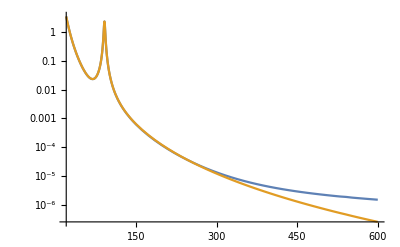

```mathematica
pltσdiff=LogPlot[{σNP[mll^2],σSM[mll^2]},{mll,20,600},
	Epilog->Inset[
		HighPTLogo[],
		Scaled[{0.17,0.15}],
		Center,
		Scaled[0.22]
	]
	,
	PlotLegends->Placed[{MaTeX["\\mathrm{NP}",FontSize->14],MaTeX["\\mathrm{SM}",FontSize->14]},{Right,Center}],
	Background->None,
	AxesLabel->{
	MaTeX["\\boldsymbol{m_{\\ell\\ell}\\,\\mathrm{[GeV]}}",FontSize->14],
	MaTeX["\\boldsymbol{\\frac{\\mathrm{d}\\sigma}{\\mathrm{d}m_{\\ell\\ell}}}\\ \\textbf{[pb]}",FontSize->14]
},
	TicksStyle->Directive[Black, 14, FontFamily->"Times"]
]
```

```mathematica
Export["DifferentialCrossSection.pdf",pltσdiff]
```

DifferentialCrossSection.pdf

## CrossSection

Computing the cross-section pp→μ^+μ^- for the invariant mass bin m_ll∈{800 GeV, 2000GeV} considering only the SM photon contribution

```mathematica
σ=CrossSection[{e[2],e[2]},
	MLLcuts->{800,2000},
	PTcuts->{0,∞},
	FF->True,
	Coefficients->{FF[Vector,{Photon,SM},_,_]}
];
```

Substituting the numerical values

```mathematica
SubstituteFF[σ,EFTorder->0,OperatorDimension->4]
Re[%]
```

0.00947613+1.3715×10^-23 ⅈ

0.00947613

Notice that some results can have a small imaginary part due to numerical artifacts. These should be removed manually by Re or Chop.

## EventYield

Can be used to turn off the printing

```mathematica
(*$PrintingProcessInfo=False*)
```

Compute the signal yield for the pp→μ^+μ^- search by CMS turning on the single Wilson coefficient [C_lq^(1)]_2211

```mathematica
NEvents=EventYield["di-muon-CMS",Coefficients->{WC["lq1",{2,2,1,1}]}];
```

```mathematica
NEvents[[-1]]//TraditionalForm
```

-(0.25866+6.38087×10^-22 ⅈ) [𝒞_lq^(1)]_2211+38.9564 ([𝒞_lq^(1)]_2211)^2+(0.00149871+1.43162×10^-19 ⅈ)

Removing imaginary parts (numerical artefacts) and printing the result in an easily readable form.

```mathematica
%//Chop//TraditionalForm
```

38.9564 ([𝒞_lq^(1)]_2211)^2-0.25866 [𝒞_lq^(1)]_2211+0.00149871

Exporting the signal yield as a python file for further analyses outside Mathematica.

```mathematica
PythonExport["di-muon-CMS",NEvents//Chop]
```

## ChiSquareLHC

Computing the χ^2 likelihood for the pp→μ^+μ^- search by CMS keeping only the two coefficients [C_lq^(1)]_2211 and [C_lq^(1)]_2222.

```mathematica
Lμμd6=ChiSquareLHC["di-muon-CMS",
	Coefficients->{WC["lq1",{2,2,1,1}],WC["lq1",{2,2,2,2}]}
];
```

Computing the projection of the χ^2 likelihood for the pp→μ^+μ^- search by CMS for the HL-LHC with an integrated luminosity of 3 ab^-1, assuimg that the error on the background prediction scales as √(3000/140).

```mathematica
Lμμd6ProjectedResacled=ChiSquareLHC["di-muon-CMS",
	Coefficients->{WC["lq1",{2,2,1,1}],WC["lq1",{2,2,2,2}]},
	Luminosity->3000,
	RescaleError->True
];
```

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

Computing the projection of the χ^2 likelihood for the pp→μ^+μ^- search by CMS for the HL-LHC with an integrated luminosity of 3 ab^-1, assuimg that the error (δBKG) on the background prediction (BKG) scales such that δBKG/BKG is constant.

```mathematica
Lμμd6ProjectedConstant=ChiSquareLHC["di-muon-CMS",
	Coefficients->{WC["lq1",{2,2,1,1}],WC["lq1",{2,2,2,2}]},
	Luminosity->3000,
	RescaleError->False
];
```

PROCESS | : | pp → μ^-μ^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 4](https://doi.org/10.17182/hepdata.101186.v2/t4)
OBSERVABLE | : | m_μμ
BINNING m_μμ [GeV] | : | {209.63,227.02,245.86,266.25,288.34,312.26,338.16,366.21,396.59,429.49,465.12,503.71,545.49,590.74,639.75,692.82,750.29,812.54,879.94,952.94,1032,1117.6,1210.3,1310.7,1419.4,1537.2,1664.7,1802.8,1952.4,2114.3,2289.7,2479.7,2685.4,2908.1,3149.4,3410.7,3693.6,4000,4500,5200,6000,7000}
EVENTS OBSERVED | : | {49128, 41800, 32648, 26435, 21188, 16797, 13170, 10490, 7650, 6128, 4613, 3457, 2635, 1979, 1478, 1016, 759, 574, 389, 295, 202, 132, 107, 71, 59, 27, 18, 13, 11, 5, 5, 4, 2, 1, 1, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 140
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

Summing all bins of each likelihood

```mathematica
Lμμd6Combined=Total[Lμμd6];
Lμμd6ProjectedResacledCombined=Total[Lμμd6ProjectedResacled];
Lμμd6ProjectedConstantCombined=Total[Lμμd6ProjectedConstant];
```

Auxiliary function to determine the Δχ^2 for m parameters and a probability p.

```mathematica
(*
m: number of fitted parameters
p: probability to contain true value
*)
Δχ2[m_Integer,p_?NumberQ]:= InverseCDF[ChiSquareDistribution[m],p];
Δχ2[2,0.95]
```

5.99146

Minimizing and plotting the 95% confidence regions for all likelihoods

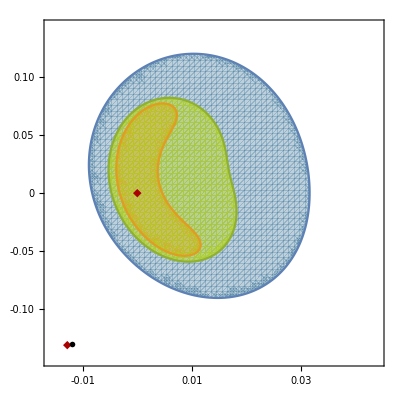

```mathematica
Lμμd6Min=NMinimize[Re[Lμμd6Combined],{WC["lq1",{2,2,1,1}],WC["lq1",{2,2,2,2}]}];
Lμμd6ProjectedResacledMin=NMinimize[Re[Lμμd6ProjectedResacledCombined],{WC["lq1",{2,2,1,1}],WC["lq1",{2,2,2,2}]}];
Lμμd6ProjectedConstantMin=NMinimize[Re[Lμμd6ProjectedConstantCombined],{WC["lq1",{2,2,1,1}],WC["lq1",{2,2,2,2}]}];

(* auxiliary function for ticks *)
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;

(* plotting *)
pltSMEFT=RegionPlot[
	{
	Re@Lμμd6Combined<=First[Lμμd6Min]+6,
	Re@Lμμd6ProjectedResacledCombined<=First[Lμμd6ProjectedResacledMin]+6,
	Re@Lμμd6ProjectedConstantCombined<=First[Lμμd6ProjectedConstantMin]+6
	}
	,
	{WC["lq1",{2,2,1,1}],-0.016,+0.044},
	{WC["lq1",{2,2,2,2}],-0.143,+0.143}
	,
PlotPoints->60,
Background->White,
FrameLabel->{
MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{2211}",FontSize->18],
MaTeX["[\\mathcal{C}_{lq}^{(1)}]_{2222}", FontSize->18]
},
FrameTicks->{{tickFunc,Automatic},{tickFunc,Automatic}},FrameTicksStyle->Directive[Black,16,Thickness[0.005],FontFamily->"CMU Serif"],FrameStyle->Directive[Black,Thickness[0.005]],
Epilog->{
Inset[Style[◆,Darker@Red],{0,0}],
	Inset[HighPTLogo[],Scaled[{0.95,0.93}],Right,Scaled[0.20]],
	Inset[MaTeX["\\boldsymbol{\\Lambda=1\,\\mathrm{TeV}}",FontSize->18]/.(Graphics[args___]:>Graphics[args,Background->Directive[White,Opacity[0.7]]]),Scaled[{0.04,0.93}],Left,Scaled[0.28]],
Inset[Style[◆,Darker@Red],{-0.013,-0.13}],
	Inset[MaTeX["\\boldsymbol{\\mathrm{SM}}",FontSize->16],{-0.012,-0.13},Left]
},
PlotStyle->{
Directive[RGBColor[0.36,0.54,0.66],Opacity[0.4]],
	Directive[RGBColor[0.93,0.57,0.13],Opacity[0.4]],
	Directive[RGBColor[0.70,0.83,0.10],Opacity[0.4]]
},
PlotLegends->Placed[SwatchLegend[
Automatic,
{
		MaTeX["\\boldsymbol{140\\,\\mathrm{fb}^{-1}}",FontSize->12],
		MaTeX["\\boldsymbol{3000\\,\\mathrm{fb}^{-1}}",FontSize->12],
		MaTeX["\\boldsymbol{3000\\,\\mathrm{fb}^{-1}}",FontSize->12]
},
LegendFunction->None,
LegendLabel->MaTeX["\\boldsymbol{95\\%\\,\\mathrm{CL}}",FontSize->12]
	],{Right,Bottom}]
]
```

```mathematica
Export["dimuon_projection.png",pltSMEFT,ImageResolution->400]
```

dimuon_projection.png

### CKM rotations

Here we compare the constraints obtained by assuming up or down alignment with the case of a diagonal CKM matrix

Choose Wilson coefficients that are used for the fit

```mathematica
wc={WC["ledq",{2,2,2,2}],WC["lequ1",{2,2,2,2}]};
```

Derive likelihood for up alignment

```mathematica
DefineBasisAlignment["up"];
Lup=Total[ChiSquareLHC["di-muon-CMS",Coefficients->wc]];
```

Derive likelihood for down alignment

```mathematica
DefineBasisAlignment["down"];
Ldown=Total[ChiSquareLHC["di-muon-CMS",Coefficients->wc]];
```

Derive likelihood for V_CKM=Id_(3x 3)

```mathematica
DefineParameters["Wolfenstein"->{0,0,0,0}];
Lno=Total[ChiSquareLHC["di-muon-CMS",Coefficients->wc]];
```

Reset the parameters

```mathematica
DefineParameters[];
```

Minimize all likelihoods

```mathematica
{LdownMin,LdownBest}=Echo[NMinimize[Re@Ldown,wc,Method->"RandomSearch",MaxIterations->500],"down-aligned"];
{LupMin,LupBest}=Echo[NMinimize[Re@Lup,wc,Method->"RandomSearch",MaxIterations->500],"up-aligned"];
{LnoMin,LnoBest}=Echo[NMinimize[Re@Lno,wc,Method->"RandomSearch",MaxIterations->500],"V_CKM=1"];
```

down-aligned  {13.37,{WC[ledq,{2,2,2,2}]→-2.35519×10^-9,WC[lequ1,{2,2,2,2}]→-2.66365×10^-9}}

up-aligned  {13.37,{WC[ledq,{2,2,2,2}]→-2.45736×10^-9,WC[lequ1,{2,2,2,2}]→-3.8569×10^-9}}

V_CKM=1  {13.37,{WC[ledq,{2,2,2,2}]→-1.22924×10^-9,WC[lequ1,{2,2,2,2}]→-7.57119×10^-9}}

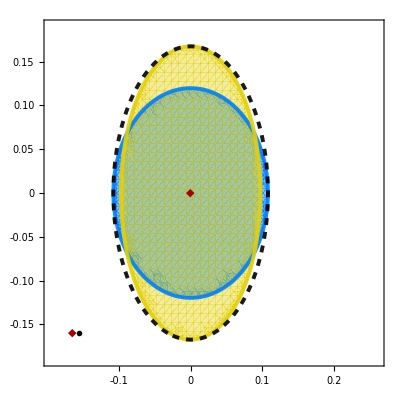

```mathematica
(* auxiliary function for ticks *)
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;
(* colors *)
$color1=RGBColor[0.00,0.5,1.00];
$color2=RGBColor[0.89,0.82,0.04];
(* Δχ^2 for confidence level p and m parameters*)
Δχ2[m_Integer,p_?NumberQ]:= InverseCDF[ChiSquareDistribution[m],p];
(* plot *)
With[{wc1=First[wc],wc2=Last[wc]},
alignmentPlot=RegionPlot[
	{
		Re@Ldown<=LdownMin+Δχ2[2,0.95],
		Re@Lup<=LupMin+Δχ2[2,0.95],
		Re@Lno <=LnoMin+Δχ2[2,0.95]
	},
	{wc1,-0.2,+0.3},{wc2,-0.25,+0.25},
	Background->White,
	FrameLabel->{
		MaTeX["[\\mathcal{C}_{ledq}]_{2222}",FontSize->20],
		MaTeX["[\\mathcal{C}_{lequ}^{(1)}]_{2222}",FontSize->20]
	},
	FrameTicks->{{tickFunc,Automatic},{tickFunc,Automatic}},
	FrameTicksStyle->Directive[Black,16,Thickness[0.005],FontFamily->"CMU Serif"],
	FrameStyle->Directive[Black,Thickness[0.005]],
	Epilog->{
		Inset[Style[◆,Darker@Red],{0,0}],
		Inset[HighPTLogo[],Scaled[{0.95,0.93}],Right,Scaled[0.20]],
		Inset[MaTeX["\\boldsymbol{\\Lambda=1\,\\mathrm{TeV}}",FontSize->18]/.(Graphics[args___]:>Graphics[args,Background->Directive[White,Opacity[0.7]]]),Scaled[{0.04,0.93}],Left,Scaled[0.28]],
	Inset[Style[◆,Darker@Red],{-0.165,-0.16}],
		Inset[MaTeX["\\boldsymbol{\\mathrm{SM}}",FontSize->16],{-0.155,-0.16},Left]
	},
	PlotLegends->Placed[SwatchLegend[
		{
			Directive[$color1,Opacity[0.7]],
			Directive[$color2,Opacity[0.7]],
			Black
		}
		,
		{
			MaTeX["\\textbf{down-aligned}",FontSize->12],
			MaTeX["\\textbf{up-aligned}",FontSize->12],
			MaTeX["\\boldsymbol{V_\\text{CKM}=\\mathds{1}_{3\\times 3}}",FontSize->12]
		}]
		,
		{Right,Bottom}
	],
	PlotStyle->{
		Directive[$color1,Opacity[0.5]],
		Directive[$color2,Opacity[0.4]],
		None
		(*Directive[Gray,Opacity[0.2]]*)
	},
	BoundaryStyle->{
		1->Directive[$color1,Opacity[0.9],Thickness[0.007],CapForm["Butt"]],
		2->Directive[$color2,Opacity[0.9],Thickness[0.007],CapForm["Butt"]],
		3->Directive[Black,Opacity[0.9], Dashed,Thickness[0.007],CapForm["Butt"]]
	},
	PlotPoints->50,
	PlotRange->{{-0.195,0.26},{-0.19,0.19}}
]
]
```

Exporting the figure

```mathematica
Export["basis_alignment.png",alignmentPlot,ImageResolution->400]
```

basis_alignment.png

## Mediators

## Initialization

Initializing the mediator mode for a S_3 scalar leptoquark with mass 2TeV and zero width

```mathematica
InitializeModel[{"S3",2000,0}]
```

Initialized mediator mode:

s-channel: <|Photon→{0,0,{s},{NC},{Vector}},ZBoson→{91.1876,2.4952,{s},{NC},{Vector}},WBoson→{79.8244,2.085,{s},{CC},{Vector}}|>

t-channel: <||>

u-channel: <|S3→{2000,0,{u},{NC,CC},{Vector}}|>

## S_3 example

Constructing the  χ^2 likelihood for the di-tau and mono-tau searches by ATLAS.

```mathematica
χSqS3ττ=ChiSquareLHC["di-tau-ATLAS"];
```

```mathematica
χSqS3τν=ChiSquareLHC["mono-tau-ATLAS"];
```

Summing all bins of the likelihoods

```mathematica
χSqS3=Total[χSqS3ττ]+Total[χSqS3τν];
```

Selecting the relevant couplings

```mathematica
LS3=SelectTerms[χSqS3,{Coupling["y3L",{2|3,3}]}];
```

Taking the real part of the likelihood (might be required for minimization)

```mathematica
LS3=Re[LS3];
```

Minimizing the likelihood

```mathematica
MinS3=NMinimize[LS3,{Coupling["y3L",{2,3}],Coupling["y3L",{3,3}]}]
```

{11.5053,{Coupling[y3L,{2,3}]→1.17123×10^-11,Coupling[y3L,{3,3}]→2.07669×10^-10}}

Plotting the 95% confidence regions

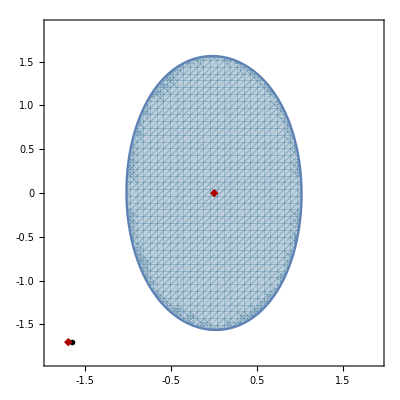

```mathematica
(* auxiliary function for ticks *)
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.03,.015}][##]&;
(* plotting *)
pltS3=RegionPlot[
LS3<=First@MinS3+5.99,
{Coupling["y3L",{2,3}],-1.9,+1.9},{Coupling["y3L",{3,3}],-1.9,+1.9}
,
PlotPoints->50,
Background->White,
FrameLabel->{
		MaTeX["[y_3^L]_{23}",FontSize->18],
		MaTeX["[y_3^L]_{33}",FontSize->18]
},
FrameTicks->{{tickFunc,Automatic},{tickFunc,Automatic}},FrameTicksStyle->Directive[Black,16,Thickness[0.005],FontFamily->"CMU Serif"],FrameStyle->Directive[Black,Thickness[0.005]],
Epilog->{
		Inset[Style[◆,Darker@Red],{0,0}],
		Inset[HighPTLogo[],Scaled[{0.95,0.93}],Right,Scaled[0.20]],
		Inset[MaTeX["\\boldsymbol{m_{S_3}=2\,\\mathrm{TeV}}",FontSize->18]/.(Graphics[args___]:>Graphics[args,Background->Directive[White,Opacity[0.7]]]),Scaled[{0.04,0.93}],Left,Scaled[0.28]],
	Inset[Style[◆,Darker@Red],{-1.7,-1.7}],
		Inset[MaTeX["\\boldsymbol{\\mathrm{SM}}",FontSize->16],{-1.65,-1.7},Left]
	},
PlotStyle->Directive[RGBColor[0.36,0.54,0.66],Opacity[0.4]],PlotLegends->Placed[MaTeX["95\\%\\,\\mathrm{CL}",FontSize->16],Scaled[{0.87,0.07}]],FrameTicksStyle->Directive[Black, 14, FontFamily->"Times"]
]
```

```mathematica
Export["ditau_S3.png",pltS3,ImageResolution->400]
```

ditau_S3.png

## Auxiliary material

## Defining parameters

## Changing the PDF set

List all available PDF sets

```mathematica
SetPDF[]
```

{PDF4LHC15,PDF4LHC21,NNPDF40,NNPDF31,CT18NNLO}

The average PDF is used for each PDF set.

A different PDF can be chosen e.g. by

```mathematica
SetPDF["NNPDF40"]
```

## Using form factors

Show for example how to extract the SM photon cross section?